{{α[t]→InterpolatingFunction[…][t],β[t]→InterpolatingFunction[…][t],γ[t]→InterpolatingFunction[…][t],α1[t]→InterpolatingFunction[…][t],β1[t]→InterpolatingFunction[…][t],γ1[t]→InterpolatingFunction[…][t]}}

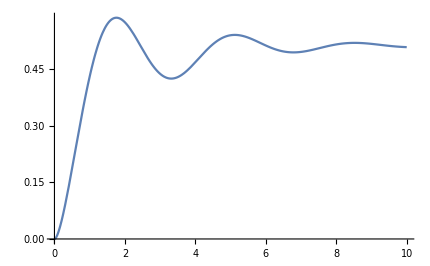

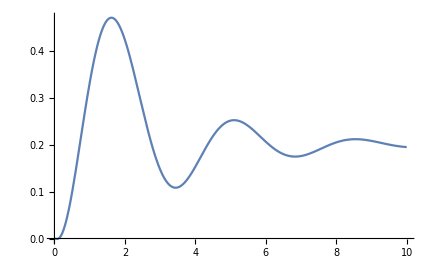

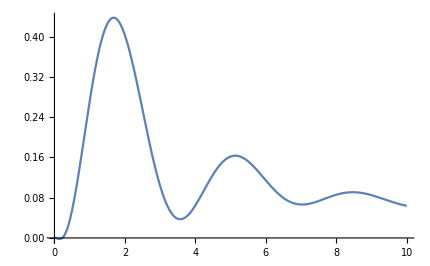

```mathematica
g=9.81;
Subscript[m, BA]=1;
Subscript[m, CB]=1;
Subscript[m, OC]=1;
Subscript[J1, BA]=1;(*Относительно точки B*)
Subscript[J1, CB]=1;(*Относительно точки C*)
Subscript[J1, OC]=1;(*Относительно точки O*)
Subscript[J, BA]=(Subscript[J1, BA]+Subscript[m, BA]*Subscript[k, BA]^2);(*Относительно центра масс BA*)
Subscript[J, CB]=(Subscript[J1, CB]+Subscript[m, CB]*Subscript[k, CB]^2);(*Относительно центра масс CB*)
Subscript[J, OC]=(Subscript[J1, OC]+Subscript[m, OC]*Subscript[k, OC]^2);(*Относительно центра масс OC*)
Subscript[l, BA]=0.2;
Subscript[l, CB]=1;
Subscript[l, OC]=1;
Subscript[k, BA]=0.1;(*Расстояние от B о центра масс звена BA*)
Subscript[k, CB]=0.5;(*Расстояние от С о центра масс звена CB*)
Subscript[k, OC]=0.5;(*Расстояние от O о центра масс звена OC*)

q=15 - 10*α1[t]; (*Равнодействующий момент сил между подвесом и бедром, "- 6*α1[t]" - момент вязкого трения*)
u=3    - 10*(β1[t] - α1[t]);(*Равнодействующий момент сил между бедром и голенью "- 6*β1[t]" - момент вязкого трения*)
s=0  - 10*(γ1[t] - β1[t]); (*Равнодействующий момент сил между голенью и стопой "- 6*γ1[t]" - момент вязкого трения*)
eqns={
α1[t]==α'[t],
β1[t]==β'[t],
γ1[t]==γ'[t],
(Subscript[J, BA] (2 β1[t]^2 Sin[α[t]-β[t]] Subscript[l, CB]^3 Subscript[l, OC] Subscript[m, BA]+2 Cos[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC] Subscript[m, CB] (-s+u+Subscript[k, CB] (-g Sin[β[t]]+α1[t]^2 Sin[α[t]-β[t]] Subscript[l, OC]) Subscript[m, CB])-2 Cos[α[t]-β[t]] Subscript[l, CB] Subscript[l, OC] (s-u+Subscript[k, CB] (γ1[t]^2 Sin[β[t]-γ[t]] Subscript[k, BA]-2 α1[t]^2 Sin[α[t]-β[t]] Subscript[l, OC]+g Sin[β[t]] (1+Subscript[m, BA])) Subscript[m, CB])+2 Subscript[J, CB] (-q+u+Subscript[l, OC] (γ1[t]^2 Sin[α[t]-γ[t]] Subscript[k, BA]+g Sin[α[t]] (Subscript[m, BA]+Subscript[m, CB])+β1[t]^2 Sin[α[t]-β[t]] (Subscript[l, CB]+Subscript[k, CB] Subscript[m, CB]))+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC])+Subscript[l, CB]^2 (α1[t]^2 Sin[2 (α[t]-β[t])] Subscript[l, OC]^2+2 γ1[t]^2 Subscript[k, BA] Subscript[l, OC] (-Cos[α[t]-β[t]] Sin[β[t]-γ[t]]+Sin[α[t]-γ[t]] Subscript[m, BA])+2 Subscript[l, OC] Subscript[m, BA] (-g Cos[α[t]-β[t]] Sin[β[t]]+g Sin[α[t]] Subscript[m, BA]+(g Sin[α[t]]+β1[t]^2 Sin[α[t]-β[t]] Subscript[k, CB]) Subscript[m, CB])+2 Subscript[m, BA] (-q+u+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC])))-Subscript[k, BA] (2 γ1[t]^2 Cos[β[t]-γ[t]] Sin[α[t]-β[t]] Subscript[k, BA]^2 Subscript[l, CB]^2 Subscript[l, OC]+s Subscript[l, OC] (-2 Cos[α[t]-γ[t]] Subscript[J, CB]+Subscript[l, CB] (Subscript[l, CB] (Cos[α[t]-γ[t]]+Cos[α[t]-2 β[t]+γ[t]]-2 Cos[α[t]-γ[t]] Subscript[m, BA])+2 Cos[α[t]-β[t]] Cos[β[t]-γ[t]] Subscript[k, CB] Subscript[m, CB]))+Subscript[k, BA] (2 β1[t]^2 Subscript[l, CB]^3 Subscript[l, OC] (Cos[β[t]-γ[t]] Sin[α[t]-γ[t]]-Cos[α[t]-γ[t]] Sin[β[t]-γ[t]] Subscript[m, BA])+2 Cos[α[t]-γ[t]] Subscript[J, CB] Subscript[l, OC] (-α1[t]^2 Sin[α[t]-γ[t]] Subscript[l, OC]+g Sin[γ[t]] Subscript[m, BA])+Subscript[l, CB] Subscript[l, OC] (-2 Cos[α[t]-γ[t]] ((s-u) Cos[β[t]-γ[t]]+β1[t]^2 Sin[β[t]-γ[t]] Subscript[J, CB])+Subscript[k, CB] (α1[t]^2 (Sin[2 (α[t]-β[t])]+Sin[2 (α[t]-γ[t])]) Subscript[l, OC]-2 g Cos[β[t]-γ[t]] (Cos[α[t]-γ[t]] Sin[β[t]]+Cos[α[t]-β[t]] Sin[γ[t]] Subscript[m, BA])) Subscript[m, CB])+Subscript[l, CB]^2 (α1[t]^2 Subscript[l, OC]^2 (Sin[2 (α[t]-β[t])]+Sin[2 (α[t]-γ[t])]-Sin[2 (α[t]-γ[t])] Subscript[m, BA])+Subscript[l, OC] (g Subscript[m, BA] (Sin[α[t]-2 β[t]]+Sin[α[t]-2 γ[t]]+2 Cos[α[t]-γ[t]] Sin[γ[t]] Subscript[m, BA])+2 Cos[β[t]-γ[t]] (g Cos[β[t]-γ[t]] Sin[α[t]]+β1[t]^2 Sin[α[t]-γ[t]] Subscript[k, CB]) Subscript[m, CB])+2 Cos[β[t]-γ[t]]^2 (-q+u+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC])))))/(2 Subscript[J, BA] (Cos[α[t]-β[t]]^2 Subscript[l, CB]^2 Subscript[l, OC]^2-(Subscript[J, CB]+Subscript[l, CB]^2 Subscript[m, BA]) (Subscript[J, OC]+Subscript[l, OC]^2 Subscript[m, BA])-Subscript[l, OC]^2 (Subscript[J, CB]+Subscript[l, CB] (-2 Cos[α[t]-β[t]]^2 Subscript[k, CB]+Subscript[l, CB] Subscript[m, BA])) Subscript[m, CB]+Cos[α[t]-β[t]]^2 Subscript[k, CB]^2 Subscript[l, OC]^2 Subscript[m, CB]^2)+Subscript[k, BA]^2 (2 Cos[β[t]-γ[t]]^2 Subscript[J, OC] Subscript[l, CB]^2+Subscript[l, OC]^2 (2 Cos[α[t]-γ[t]]^2 Subscript[J, CB]+Subscript[l, CB] (Subscript[l, CB] (-4 Cos[α[t]-β[t]] Cos[α[t]-γ[t]] Cos[β[t]-γ[t]]+(2+Cos[2 (α[t]-γ[t])]+Cos[2 (β[t]-γ[t])]) Subscript[m, BA])+2 Cos[β[t]-γ[t]] (-2 Cos[α[t]-β[t]] Cos[α[t]-γ[t]] Subscript[k, CB]+Cos[β[t]-γ[t]] Subscript[l, CB]) Subscript[m, CB]))))==α1'[t],
(Subscript[J, BA] (2 Subscript[J, OC] (s-u+Subscript[l, CB] (γ1[t]^2 Sin[β[t]-γ[t]] Subscript[k, BA]-α1[t]^2 Sin[α[t]-β[t]] Subscript[l, OC]+g Sin[β[t]] Subscript[m, BA])+Subscript[k, CB] (g Sin[β[t]]-α1[t]^2 Sin[α[t]-β[t]] Subscript[l, OC]) Subscript[m, CB])-Subscript[l, OC] (β1[t]^2 Sin[2 (α[t]-β[t])] Subscript[l, CB]^2 Subscript[l, OC]+2 Subscript[l, CB] (α1[t]^2 Sin[α[t]-β[t]] Subscript[l, OC]^2 (Subscript[m, BA]+Subscript[m, CB])+Subscript[l, OC] (g Subscript[m, BA] (Cos[α[t]-β[t]] Sin[α[t]]-Sin[β[t]] Subscript[m, BA])+(g Cos[α[t]-β[t]] Sin[α[t]]+β1[t]^2 Sin[2 (α[t]-β[t])] Subscript[k, CB]-g Sin[β[t]] Subscript[m, BA]) Subscript[m, CB])+γ1[t]^2 Subscript[k, BA] Subscript[l, OC] (Cos[α[t]-β[t]] Sin[α[t]-γ[t]]-Sin[β[t]-γ[t]] (Subscript[m, BA]+Subscript[m, CB]))+Cos[α[t]-β[t]] (-q+u+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC]))+2 (α1[t]^2 Sin[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC]^2 Subscript[m, CB] (Subscript[m, BA]+Subscript[m, CB])+Subscript[l, OC] (Subscript[m, BA] (-s+u+g Cos[α[t]] Sin[α[t]-β[t]] Subscript[k, CB] Subscript[m, CB])+Subscript[m, CB] (-s+u+Subscript[k, CB] (γ1[t]^2 Cos[α[t]-β[t]] Sin[α[t]-γ[t]] Subscript[k, BA]+Sin[α[t]-β[t]] (g Cos[α[t]]+β1[t]^2 Cos[α[t]-β[t]] Subscript[k, CB]) Subscript[m, CB])))+Cos[α[t]-β[t]] Subscript[k, CB] Subscript[m, CB] (-q+u+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC]))))+Subscript[k, BA] (2 Cos[β[t]-γ[t]] Subscript[J, OC] Subscript[l, CB] (s+Subscript[k, BA] (β1[t]^2 Sin[β[t]-γ[t]] Subscript[l, CB]+α1[t]^2 Sin[α[t]-γ[t]] Subscript[l, OC]-g Sin[γ[t]] Subscript[m, BA]))+Subscript[l, OC] (2 γ1[t]^2 Cos[α[t]-γ[t]] Sin[α[t]-β[t]] Subscript[k, BA]^2 Subscript[l, CB] Subscript[l, OC]+2 s Subscript[l, OC] (-Cos[α[t]-β[t]] Cos[α[t]-γ[t]] Subscript[k, CB] Subscript[m, CB]+Subscript[l, CB] (-Cos[α[t]-β[t]] Cos[α[t]-γ[t]]+Cos[β[t]-γ[t]] (Subscript[m, BA]+Subscript[m, CB])))+Subscript[k, BA] (2 Cos[α[t]-γ[t]] Subscript[l, OC] ((-s+u) Cos[α[t]-γ[t]]-Subscript[k, CB] (g Cos[α[t]-γ[t]] Sin[β[t]]+α1[t]^2 Sin[β[t]-γ[t]] Subscript[l, OC]-g Cos[α[t]-β[t]] Sin[γ[t]] Subscript[m, BA]) Subscript[m, CB])+β1[t]^2 Subscript[l, CB]^2 Subscript[l, OC] (2 Cos[α[t]-γ[t]] Sin[α[t]-2 β[t]+γ[t]]+Sin[2 (β[t]-γ[t])] (Subscript[m, BA]+Subscript[m, CB]))+2 Subscript[l, CB] (Subscript[l, OC] (g Subscript[m, BA] (Cos[α[t]-γ[t]] Sin[α[t]-β[t]+γ[t]]-Cos[β[t]-γ[t]] Sin[γ[t]] Subscript[m, BA])+(β1[t]^2 Cos[α[t]-γ[t]] Sin[α[t]-2 β[t]+γ[t]] Subscript[k, CB]+g Cos[β[t]-γ[t]] (Cos[α[t]-γ[t]] Sin[α[t]]-Sin[γ[t]] Subscript[m, BA])) Subscript[m, CB])+α1[t]^2 Subscript[l, OC]^2 (-Cos[α[t]-γ[t]] Sin[β[t]-γ[t]]+Cos[β[t]-γ[t]] Sin[α[t]-γ[t]] (Subscript[m, BA]+Subscript[m, CB]))+Cos[α[t]-γ[t]] Cos[β[t]-γ[t]] (-q+u+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC]))))))/(2 Subscript[J, BA] (Cos[α[t]-β[t]]^2 Subscript[l, CB]^2 Subscript[l, OC]^2-(Subscript[J, CB]+Subscript[l, CB]^2 Subscript[m, BA]) (Subscript[J, OC]+Subscript[l, OC]^2 Subscript[m, BA])-Subscript[l, OC]^2 (Subscript[J, CB]+Subscript[l, CB] (-2 Cos[α[t]-β[t]]^2 Subscript[k, CB]+Subscript[l, CB] Subscript[m, BA])) Subscript[m, CB]+Cos[α[t]-β[t]]^2 Subscript[k, CB]^2 Subscript[l, OC]^2 Subscript[m, CB]^2)+Subscript[k, BA]^2 (2 Cos[β[t]-γ[t]]^2 Subscript[J, OC] Subscript[l, CB]^2+Subscript[l, OC]^2 (2 Cos[α[t]-γ[t]]^2 Subscript[J, CB]+Subscript[l, CB] (Subscript[l, CB] (-4 Cos[α[t]-β[t]] Cos[α[t]-γ[t]] Cos[β[t]-γ[t]]+(2+Cos[2 (α[t]-γ[t])]+Cos[2 (β[t]-γ[t])]) Subscript[m, BA])+2 Cos[β[t]-γ[t]] (-2 Cos[α[t]-β[t]] Cos[α[t]-γ[t]] Subscript[k, CB]+Cos[β[t]-γ[t]] Subscript[l, CB]) Subscript[m, CB]))))==β1'[t],
(Subscript[J, OC] Subscript[l, CB] (-γ1[t]^2 Sin[2 (β[t]-γ[t])] Subscript[k, BA]^2 Subscript[l, CB]-2 s Subscript[l, CB] Subscript[m, BA]+2 Subscript[k, BA] (-β1[t]^2 Sin[β[t]-γ[t]] Subscript[l, CB]^2 Subscript[m, BA]+Subscript[l, CB] (α1[t]^2 Subscript[l, OC] (Cos[β[t]-γ[t]] Sin[α[t]-β[t]]-Sin[α[t]-γ[t]] Subscript[m, BA])+g Subscript[m, BA] (-Cos[β[t]-γ[t]] Sin[β[t]]+Sin[γ[t]] Subscript[m, BA]))+Cos[β[t]-γ[t]] (-s+u+Subscript[k, CB] (-g Sin[β[t]]+α1[t]^2 Sin[α[t]-β[t]] Subscript[l, OC]) Subscript[m, CB])))-Subscript[J, CB] (2 Subscript[J, OC] (s+Subscript[k, BA] (β1[t]^2 Sin[β[t]-γ[t]] Subscript[l, CB]+α1[t]^2 Sin[α[t]-γ[t]] Subscript[l, OC]-g Sin[γ[t]] Subscript[m, BA]))+Subscript[l, OC] (γ1[t]^2 Sin[2 (α[t]-γ[t])] Subscript[k, BA]^2 Subscript[l, OC]+2 s Subscript[l, OC] (Subscript[m, BA]+Subscript[m, CB])+2 Subscript[k, BA] (α1[t]^2 Sin[α[t]-γ[t]] Subscript[l, OC]^2 (Subscript[m, BA]+Subscript[m, CB])+Subscript[l, OC] (g Subscript[m, BA] (Cos[α[t]-γ[t]] Sin[α[t]]-Sin[γ[t]] Subscript[m, BA])+(Cos[α[t]-γ[t]] (g Sin[α[t]]+β1[t]^2 Sin[α[t]-β[t]] Subscript[k, CB])-g Sin[γ[t]] Subscript[m, BA]) Subscript[m, CB])+β1[t]^2 Subscript[l, CB] Subscript[l, OC] (Cos[α[t]-γ[t]] Sin[α[t]-β[t]]+Sin[β[t]-γ[t]] (Subscript[m, BA]+Subscript[m, CB]))+Cos[α[t]-γ[t]] (-q+u+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC]))))+Subscript[l, OC] (γ1[t]^2 Subscript[k, BA]^2 Subscript[l, CB] Subscript[l, OC] (2 Cos[α[t]-β[t]] Sin[α[t]+β[t]-2 γ[t]] Subscript[k, CB] Subscript[m, CB]+Subscript[l, CB] (-2 Cos[α[t]-β[t]] Sin[α[t]+β[t]-2 γ[t]] (-1+Subscript[m, BA])-Sin[2 (β[t]-γ[t])] Subscript[m, CB]))+2 s Subscript[l, OC] (2 Cos[α[t]-β[t]]^2 Subscript[k, CB] Subscript[l, CB] Subscript[m, CB]+Cos[α[t]-β[t]]^2 Subscript[k, CB]^2 Subscript[m, CB]^2+Subscript[l, CB]^2 (Cos[α[t]-β[t]]^2-Subscript[m, BA] (Subscript[m, BA]+Subscript[m, CB])))+Subscript[k, BA] (2 Cos[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC] Subscript[m, CB] ((s-u) Cos[α[t]-γ[t]]+Subscript[k, CB] (g Cos[α[t]-γ[t]] Sin[β[t]]+α1[t]^2 Sin[β[t]-γ[t]] Subscript[l, OC]-g Cos[α[t]-β[t]] Sin[γ[t]] Subscript[m, BA]) Subscript[m, CB])+2 β1[t]^2 Subscript[l, CB]^3 Subscript[l, OC] (Cos[α[t]-β[t]] Sin[α[t]-γ[t]]-Subscript[m, BA] (Cos[α[t]-γ[t]] Sin[α[t]-β[t]]+Sin[β[t]-γ[t]] (Subscript[m, BA]+Subscript[m, CB])))+Subscript[l, CB]^2 (Subscript[l, OC] (2 g (-1+Subscript[m, BA]) Subscript[m, BA] (-Cos[α[t]-β[t]] Sin[α[t]+β[t]-γ[t]]+Sin[γ[t]] Subscript[m, BA])+(2 Cos[α[t]-β[t]] (g Cos[β[t]-γ[t]] Sin[α[t]]+2 β1[t]^2 Sin[α[t]-γ[t]] Subscript[k, CB])-(g (Sin[2 α[t]-γ[t]]+Sin[2 β[t]-γ[t]]+2 Sin[γ[t]])+2 β1[t]^2 Cos[α[t]-γ[t]] Sin[α[t]-β[t]] Subscript[k, CB]) Subscript[m, BA]+2 g Sin[γ[t]] Subscript[m, BA]^2) Subscript[m, CB])+α1[t]^2 Subscript[l, OC]^2 (2 Cos[α[t]-β[t]] Sin[β[t]-γ[t]]+(Sin[α[t]-γ[t]]+Sin[α[t]-2 β[t]+γ[t]]-2 Sin[α[t]-γ[t]] Subscript[m, BA]) (Subscript[m, BA]+Subscript[m, CB]))+(Cos[α[t]-γ[t]]+Cos[α[t]-2 β[t]+γ[t]]-2 Cos[α[t]-γ[t]] Subscript[m, BA]) (-q+u+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC]))+Subscript[l, CB] (Subscript[l, OC] (2 (s-u) (Cos[α[t]-β[t]] Cos[α[t]-γ[t]]-Cos[β[t]-γ[t]] Subscript[m, BA])+(2 (-s+u) Cos[β[t]-γ[t]]+g Subscript[k, CB] (2 Cos[α[t]-β[t]] Cos[α[t]-γ[t]] Sin[β[t]]+(Sin[2 α[t]-γ[t]]-(2+Cos[2 (α[t]-β[t])]) Sin[γ[t]]) Subscript[m, BA])) Subscript[m, CB]+2 Subscript[k, CB] (g Cos[α[t]] Cos[β[t]-γ[t]] Sin[α[t]-β[t]]+β1[t]^2 Cos[α[t]-β[t]] Sin[α[t]-γ[t]] Subscript[k, CB]) Subscript[m, CB]^2)+2 α1[t]^2 Subscript[k, CB] Subscript[l, OC]^2 Subscript[m, CB] (2 Cos[α[t]-β[t]] Sin[β[t]-γ[t]]+Cos[β[t]-γ[t]] Sin[α[t]-β[t]] (Subscript[m, BA]+Subscript[m, CB]))+2 Cos[α[t]-β[t]] Cos[β[t]-γ[t]] Subscript[k, CB] Subscript[m, CB] (-q+u+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC])))))/(2 Subscript[J, BA] (Cos[α[t]-β[t]]^2 Subscript[l, CB]^2 Subscript[l, OC]^2-(Subscript[J, CB]+Subscript[l, CB]^2 Subscript[m, BA]) (Subscript[J, OC]+Subscript[l, OC]^2 Subscript[m, BA])-Subscript[l, OC]^2 (Subscript[J, CB]+Subscript[l, CB] (-2 Cos[α[t]-β[t]]^2 Subscript[k, CB]+Subscript[l, CB] Subscript[m, BA])) Subscript[m, CB]+Cos[α[t]-β[t]]^2 Subscript[k, CB]^2 Subscript[l, OC]^2 Subscript[m, CB]^2)+Subscript[k, BA]^2 (2 Cos[β[t]-γ[t]]^2 Subscript[J, OC] Subscript[l, CB]^2+Subscript[l, OC]^2 (2 Cos[α[t]-γ[t]]^2 Subscript[J, CB]+Subscript[l, CB] (Subscript[l, CB] (-4 Cos[α[t]-β[t]] Cos[α[t]-γ[t]] Cos[β[t]-γ[t]]+(2+Cos[2 (α[t]-γ[t])]+Cos[2 (β[t]-γ[t])]) Subscript[m, BA])+2 Cos[β[t]-γ[t]] (-2 Cos[α[t]-β[t]] Cos[α[t]-γ[t]] Subscript[k, CB]+Cos[β[t]-γ[t]] Subscript[l, CB]) Subscript[m, CB]))))==γ1'[t],


α[0]==0,β[0]==0,γ[0]==0,α1[0]==0,β1[0]==0,γ1[0]==0

};


sol = NDSolve[eqns,{α[t],β[t],γ[t],α1[t],β1[t],γ1[t]},{t,0,20} ]
Plot[Evaluate[(α[t]/.sol)],{t,0,10},PlotRange->All]
Plot[Evaluate[(β[t]/.sol)],{t,0,10},PlotRange->All]
Plot[Evaluate[(γ[t]/.sol)],{t,0,10},PlotRange->All]
(*Plot[Evaluate[15-10*(α1[t]/.sol)],{t,0,10},PlotRange->All]
Plot[Evaluate[(3-10*β1[t]/.sol)],{t,0,10},PlotRange->All]
Plot[Evaluate[-10*(γ1[t]/.sol)],{t,0,10},PlotRange->All]*)
```